iterations = 1000, MSE = 0.00591274

{0.000903536,0.0830813,0.0830813,0.900777}

iterations = 2000, MSE = 0.00269066

{0.00025304,0.0561244,0.0561244,0.933196}

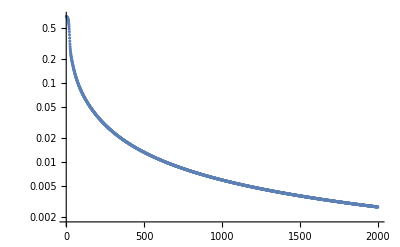

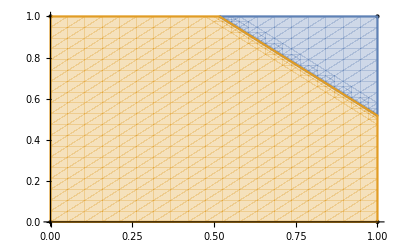

-Graphics-

```mathematica
w00 =0.5;
w11=1.5;
b1=3;
learning=1.0;
wo={w00,w11,b1};
cases={{a0->0,a1->0},{a0->0,a1->1},{a0->1,a1->0},{a0->1,a1->1}};
true={0,0,0,1};
iterations=2000;
msep=Table[0,{jj,1,iterations}];
Do[
fy=wo⟦1⟧ a0 +wo⟦1⟧ a1+wo⟦3⟧;
yii=Table[yi->fy/.{cases⟦ii⟧},{ii,1,4}];
afun=1/(1+Exp[-yi])/.yii;
g1=2/4 Table[(afun⟦ii⟧-true⟦ii⟧),{ii,1,4}];
g2=Table[afun⟦ii⟧(1-afun⟦ii⟧),{ii,1,4}];
g3=Table[{a0,a1,1}/.cases⟦ii⟧,{ii,1,4}];
dJ =Table[g1⟦ii⟧ g2⟦ii⟧ g3⟦ii⟧,{ii,1,4}];
wn=wo-learning Sum[dJ⟦ii⟧,{ii,1,4}];
wo=wn;
msep⟦jj⟧=1/4 Sum[(afun⟦i⟧-true⟦i⟧)^2,{i,1,4}];
If[Mod[jj,1000]==0.0,Print["iterations = ",jj,", MSE = ",msep⟦jj⟧];Print[afun]];
,{jj,1,iterations}]
ListLogPlot[msep,BaseStyle->{FontSize->30,FontFamily->"Times"},ImageSize->{700}]
Show[ListPlot[{a0,a1}/.cases,BaseStyle->{FontSize->30,FontFamily->"Times"},ImageSize->{700},PlotStyle->{Black,PointSize[Large]}],RegionPlot[{fy>0,fy≤0},{a0,0,1},{a1,0,1}]]
```